Question 1.

ⅇ^x

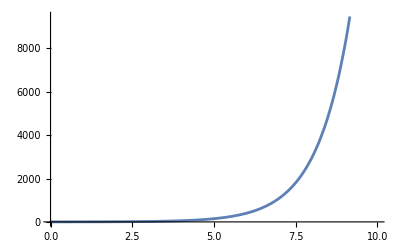

```mathematica
(*1*)f=Exp[x]
Plot[f,{x,0,10}]
(*
we use the Exp function rahter than directly using the constant e
*)
```

Sin[x]

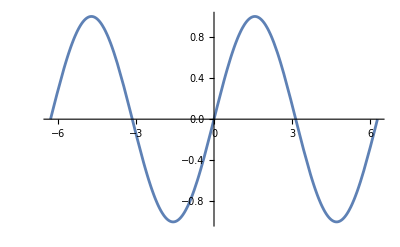

```mathematica
(*2*)g=Sin[x]
Plot[g,{x,-2 Pi,2 Pi}]
(*
there was a mistake in the brackets used.
*)
```

{t→0.876726}

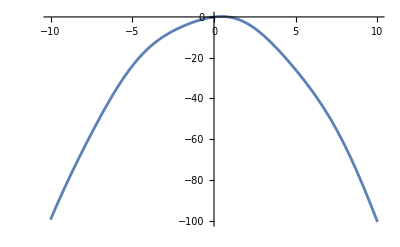

```mathematica
(*3*)FindRoot[Sin[t]==t^2,{t,1}]
Plot[Sin[t]-t^2,{t,-10,10}]
(*
== was missing in the first line and the parameter used in the 2nd line was wrong.
*)
```

```mathematica
(*4*)Manipulate[Plot[{x^n,x+n,Sqrt[x*n/7]},{x,10,0}],{n,0,10,15}]
(*there was a mistmatch of brackets.*)
```

Piecewise[{{x^2, x<0}, {x, x≥0}, {0, True}}]

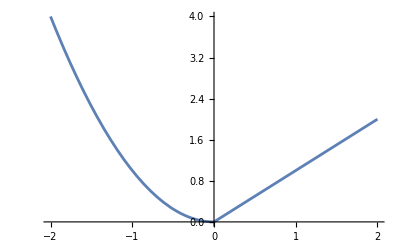

```mathematica
(*5*)k=Piecewise[{{x^2,x<0},{x,x>=0}}]
Plot[k,{x,-2,2}]
(*we assigned it to the variable k and remove the parameter x while writting the plot command.*)
```

Question 2.

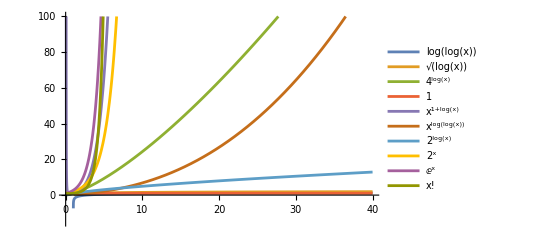

```mathematica
Plot[{Log[Log[x]],Log[x]^(1/2),4^Log[x],1,x^(1+Log[x]),x^(Log[Log[x]]),2^Log[x],2^x,f,x!},{x,0,40},PlotLegends->"Expressions",PlotRange->{-15,100}]
```

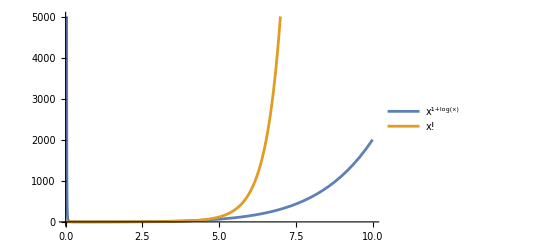

```mathematica
Plot[{x^(1+Log[x]),x!},{x,0,10},PlotLegends->"Expressions"](*
x! is the asymptotically fastest as x -> ∞, but x^(1+log[x])is asymptote @ x=0.
*)
```

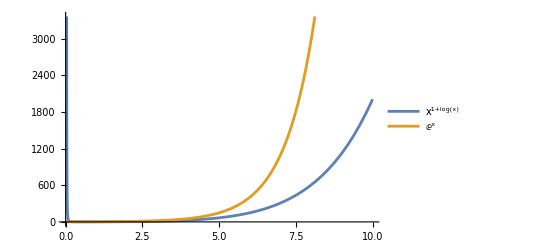

```mathematica
Plot[{x^(1+Log[x]),f},{x,0,10},PlotLegends->"Expressions"]
```

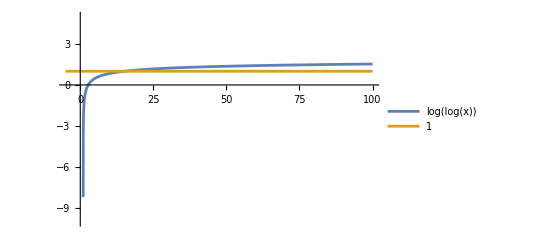

```mathematica
Plot[{Log[Log[x]],1},{x,-5,100},PlotRange->{-10,5},PlotLegends->"Expressions"](*
1 is the slowest fucnction.
*)
```

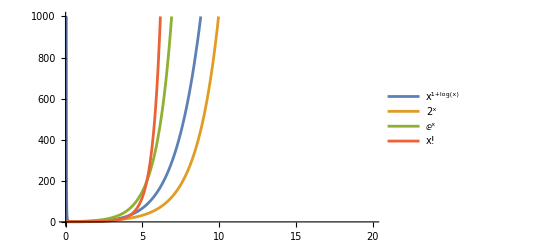

```mathematica
Plot[{x^(1+Log[x]),2^x,f,x!},{x,0,20},PlotLegends->"Expressions",PlotRange->{0,1000}]
```

ans for question 2: 1<log(log(x))<log(x)^(1/2)<2^(log(x))<x^(log(log(x))<4^log(x)<2^x<x^(1+log(x))<e^x<x!

Question 3

ⅇ^x Sin[x]

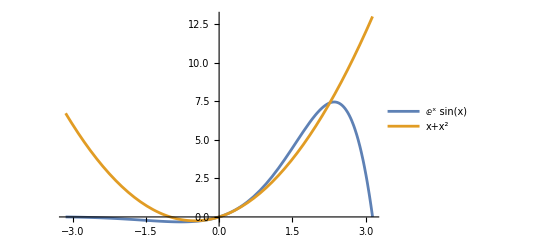

```mathematica
F=Exp[x] Sin[x]
(*taylor*)(*_*)(*Ser*)(*=*)(*Series[F,{x,0,2}]*)
Plot[{F,Evaluate[Normal[Series[F,{x,0,2}]]]},{x,-Pi, Pi},PlotLegends->"Expressions"]
```

Question 4

```mathematica
N[Pi]
```

3.14159

```mathematica
N[Pi,10]
```

3.141592654

```mathematica
N[E,10]
```

2.718281828

```mathematica
N[Pi,100]
```

3.141592653589793238462643383279502884197169399375105820974944592307816406286208998628034825342117068

```mathematica
N[2^(1/2),16]
```

1.414213562373095

```mathematica
N[2^(1/3),16]
```

1.259921049894873

Question 5

```mathematica
f1=Exp[-x/4] Cos[x]
```

ⅇ^(-x/4) Cos[x]

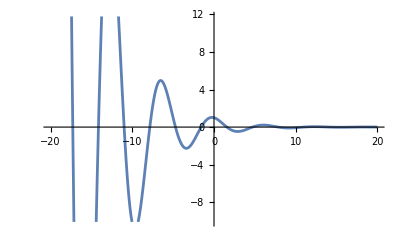

9.32103

```mathematica
Plot[f1,{x,-20,20}]
EuclideanDistance[{-3.4,-2.26},{2.8,4.7}]
```

Question 6

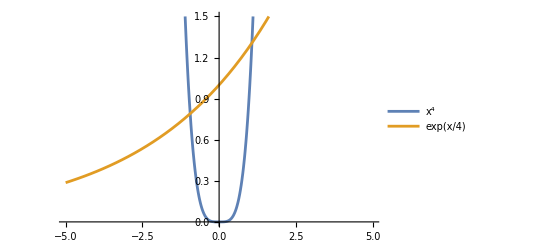

```mathematica
Plot[{x^4,Exp[x/4]},{x,-5,5},PlotLegends->"Expressions",PlotRange->{0,1.5}]
(*
POIs = -.94 and 1.07
*)
```

```mathematica
roots=Table[FindRoot[x^4==Exp[x/4],{x,guess}],{guess,-1,2}]
distinctRoots=Union[roots[[All,1]]]
```

{{x→-0.942779},{x→-0.942779},{x→1.0691},{x→1.0691}}

{x→-0.942779,x→1.0691,x→1.0691}

Question 7

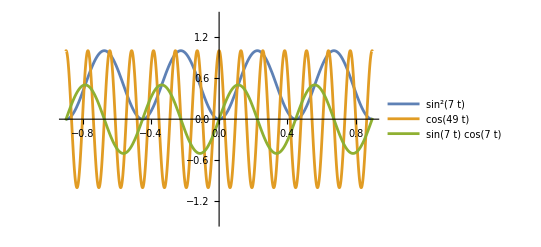

```mathematica
Plot[{(Sin[7 t])^2,Cos[49 t],Sin[7 t] Cos[7t]},{t,-0.9,0.9},PlotLegends->"Expressions",PlotRange->{-1.5,1.5}]
```